```mathematica
data={
{8,.325925},
{9,.4302},
{10,.5358},
{11,.6525},
{21,1.8}
};

line[n_]=Fit[data,{1,n},n]
```

-0.596239+0.113994 n

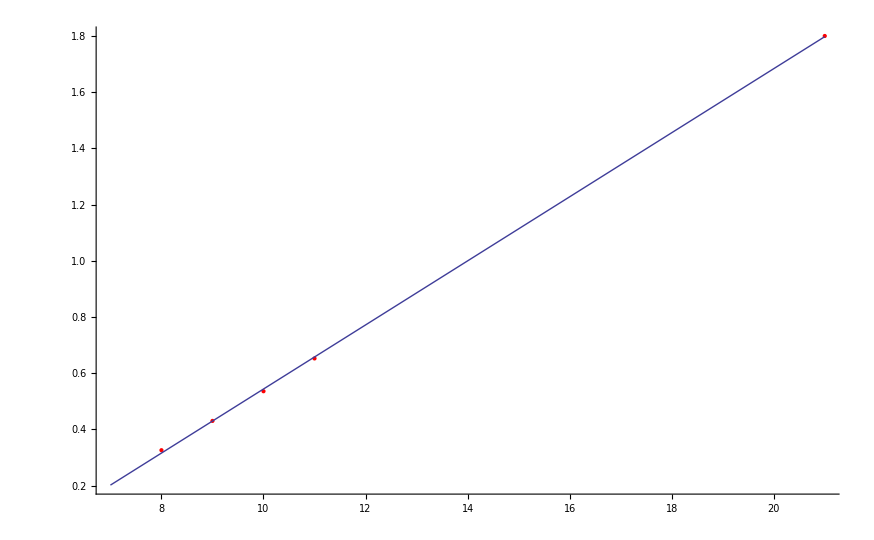

```mathematica
Show[ListPlot[data,PlotStyle->Red],Plot[line[n],{n,7,21}]]
```

```mathematica
line[21]
```

1.73423